Reading in Data . . .

Creating Data Sets . . .

Processing . . .

132.436 | 2.14403 | 0.000791567 | 109.731

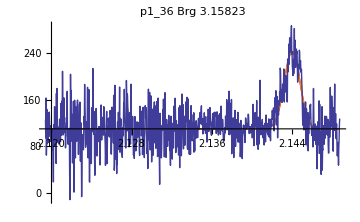

89.1929 | 2.08026 | 0.00135399 | 69.5697

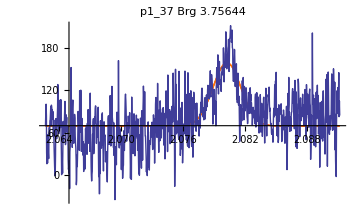

182.392 | 2.18885 | 0.000877915 | 98.907

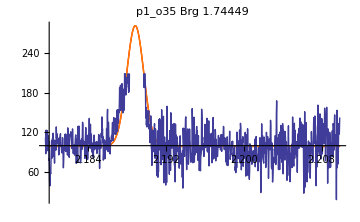

261.627 | 2.18789 | 0.00544203 | -69.2791

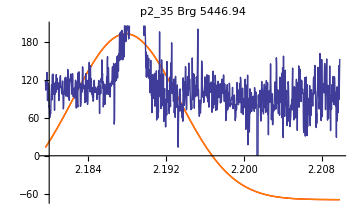

115.332 | 2.14408 | 0.000626747 | 132.548

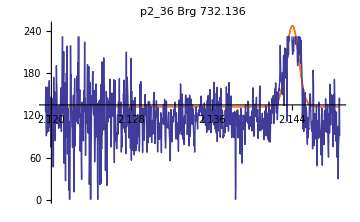

91.0101 | 2.08019 | 0.00128476 | 77.2396

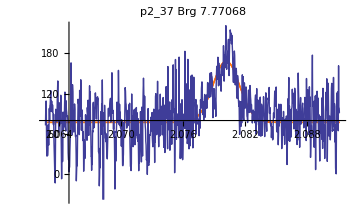

103.324 | 2.18845 | 0.000512962 | 116.91

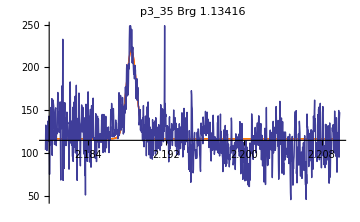

62.5748 | 2.14375 | 0.0004019 | 129.875

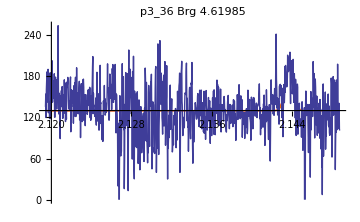

63.6924 | 2.07989 | 0.000555569 | 105.583

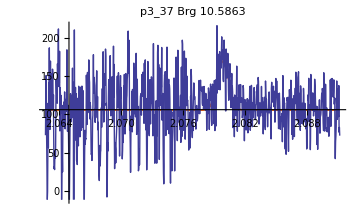

282.232 | 4.09461 | 0.0012311 | -45.4887

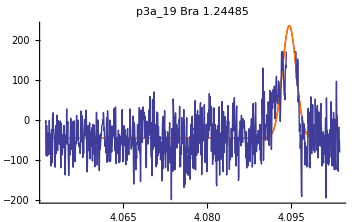

251.709 | 4.0939 | 0.00204802 | 97.6603

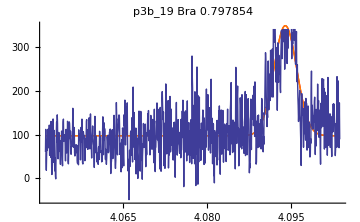

86.4826 | 4.09368 | 0.000718651 | 38.9628

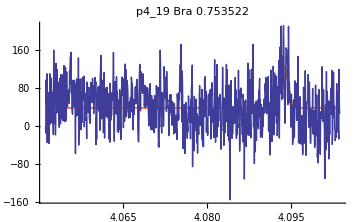

261.523 | 4.09353 | 0.000605218 | 249.01

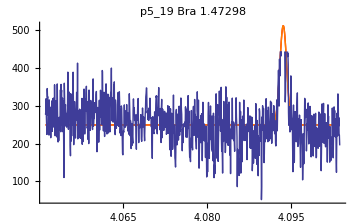

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

3472.61 | 2.40678 | -0.0559654 | 84.3855

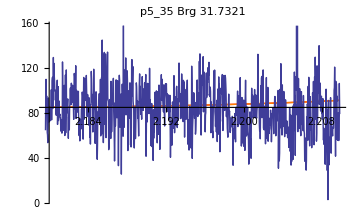

70.4327 | 2.1876 | 0.000245738 | 0.978043

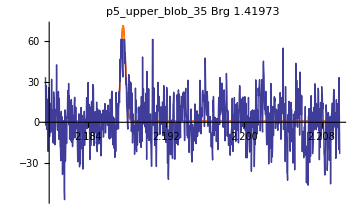

231.67 | 2.18863 | 0.00046414 | 103.198

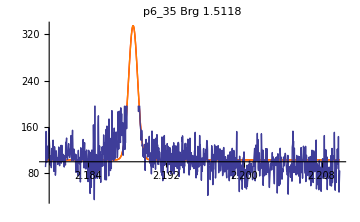

151.966 | 2.08007 | 0.000543309 | 81.8351

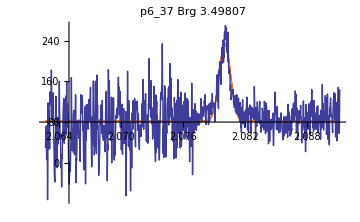

59.4783 | 4.09208 | 0.000406418 | -1.35664

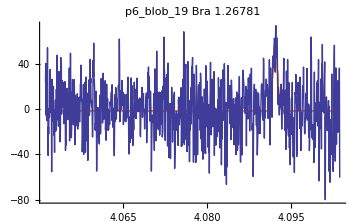

56.8077 | 2.18897 | 0.000193111 | -0.402894

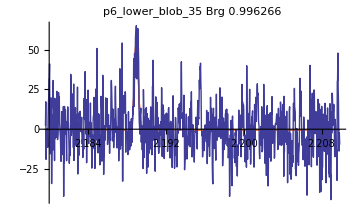

44.6291 | 2.08044 | 0.000171847 | -2.69468

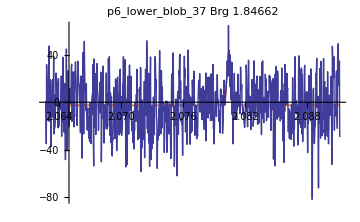

50.7228 | 2.18887 | 0.000243759 | 1.05391

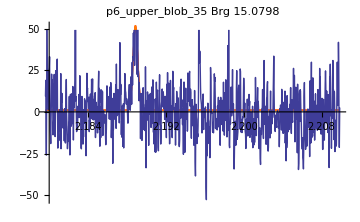

39.5455 | 2.08042 | 0.000211736 | -1.41965

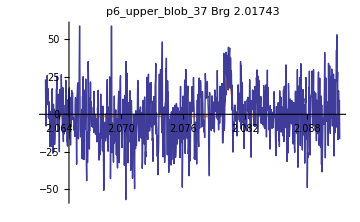

372.193 | 4.09386 | 0.000827643 | 84.3617

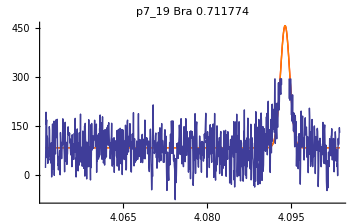

97.8113 | 2.18839 | 0.00053244 | 111.944

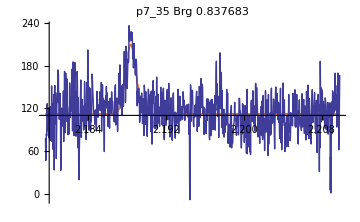

64.9094 | 2.14385 | 0.000446851 | 129.519

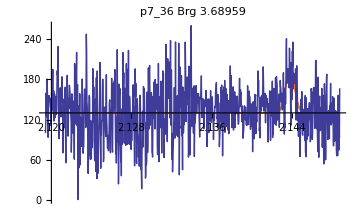

44.1961 | 2.08033 | 0.00251162 | 89.5793

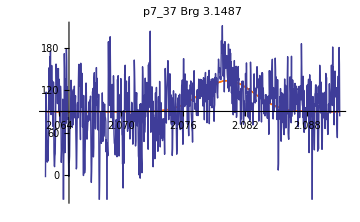

110.933 | 4.09444 | 0.000263526 | -46.37

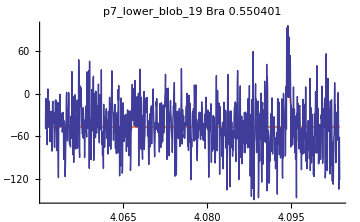

101.803 | 4.09433 | 0.000435544 | -54.9905

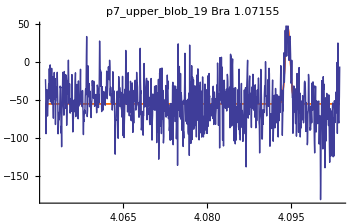

Done

```mathematica
Remove["Global`*"]
CreateXYDat[x_,y_]:=Partition[Riffle[Flatten[x],Flatten[y]],2]
Print["Reading in Data . . . "]
SetDirectory["~//REDUCTION//CSVFILES//"];
files=Sort[Flatten[Import["~//REDUCTION//CSVFILES//files.txt","CSV"] ]];
stuff=Sort[Import["~//REDUCTION//InitFile.csv"] [[All,{1,4,11,12,14,15,22,23,24,25,26,27,28,5,13,16}]]];
Print["Creating Data Sets . . . "]
numobjects:=Dimensions[files][[1]]/2 (*how many objects in the data set*)
ObjectData=Partition[files,2] ;(*Get names of files holding the data*)
finaldata=Table[CreateXYDat[Import[ObjectData[[i,1]]],Import[ObjectData[[i,2]]]],{i,1,numobjects}];
Δ=Table[StandardDeviation[finaldata[[i,stuff[[i,3]];;stuff[[i,4]],2]]],{i,1,numobjects}];
weights=Table[(1/Δ[[i]])^2,{i,1,numobjects},{j,1,Dimensions[finaldata][[2]]}];
Print["Processing . . . "]
(*Do[Print[ListLinePlot[Clip[(finaldata[[i,All,2]]-Mean[finaldata[[i,All,2]]])/Δ[[i]],{-5,12}],PlotRange->All,PlotLabel->ObjectData[[i,1]]]],{i,1,numobjects}]*)
Gauss[x_,A_,μ_,σ_]=A √(2 π)σ PDF[NormalDistribution[μ,σ],x];
function=d+Gauss[x,P1,μ1,σ1];+ Gauss[x,P2,μ2,σ2] ;
(*nlm=Table[Null,{k,1,8(*Dimensions[a][[1]]/2*)}];
fit[k]:=nlm[#]&;*)
Do[
(*nlm=NonlinearModelFit[finaldata[[k]],function,{{d,stuff[[k,13]]},{P1,stuff[[k,7]]},{μ1,stuff[[k,8]]},{σ1,stuff[[k,9]]},{P2,stuff[[k,10]]},{μ2,stuff[[k,11]]},{σ2,stuff[[k,12]]}},x,Weights->weights[[k,200;;400]], MaxIterations->10000,Method->"LevenbergMarquardt"];*)
(*fit[k]=nlm;*)
nlm=NonlinearModelFit[(*MovingMedian[*)finaldata[[k]](*,10]*),function,{{d,stuff[[k,15]]},{P1,stuff[[k,15]]},{μ1,stuff[[k,5]]},{σ1,stuff[[k,6]]}(*,{P2,stuff[[k,10]]},{μ2,stuff[[k,11]]},{σ2,stuff[[k,12]]}*)},x,Weights->weights[[k]], MaxIterations->10000,Method->"LevenbergMarquardt"];
par=nlm["BestFitParameters"];
g1[x_]=Gauss[x,P1,μ1,σ1]+d/.par;
g2[x_]=Gauss[x,P2,μ2,σ2]  +d/.par;
Print[{{P1,μ1,σ1,d}}/.par //TableForm];
gauss[x_]=Normal[nlm];
range1={x,Min[finaldata[[k,All,1]]],Max[finaldata[[k,All,1]]]};
range2={x,Min[finaldata[[k,All,1]]],Max[finaldata[[k,All,1]]]};
range3={x,μ-4 σ,μ+4σ};
p1[k]=Plot[gauss[x],{x,Min[finaldata[[k,All,1]]],Max[finaldata[[k,All,1]]]},PlotRange->All,PlotStyle->{Thick,Red},ImageSize->Medium];
p2[k]=Plot[{g1[x],g2[x]},{x,Min[finaldata[[k,All,1]]],Max[finaldata[[k,All,1]]]},PlotRange->All,PlotStyle->{{Thick,Orange},{Thick,Green}},PlotStyle->Thick,ImageSize->Medium];
datplot[k]=ListLinePlot[finaldata[[k]](*,PlotRange->All*),ImageSize->Medium];
{{p1[k]},{p2[k]},{datplot[k]}} ;
Print[Show[p1[k],p2[k],datplot[k],PlotRange->All,PlotRangeClipping->True
,PlotLabel->StringJoin[ ToString[ stuff[[k,1]]]," ",ToString[stuff[[k,2]]]," ",ToString[nlm["EstimatedVariance"]]]]];
residplot:=ListPlot[nlm["FitResiduals"]];
,{k,1,numobjects}]
Print["Done"]
(*h={P1,μ1,σ1,P2,μ1,σ2,d}/.Riffle[Table[fit[k]["BestFitParameters"],{k,{8,10,12,15}}],Table[fit[j]["BestFitParameters"],{j,{9,11,13,16}}]] //N;
Export["~//hi.csv",h,"csv"]*)
```

```mathematica
name={"aBra.pdf","aBrg.pdf","bBra.pdf","bBrg.pdf","cBra.pdf","cBrg.pdf","0","dBra.pdf","dBrg.pdf"}
Table[Export["~//"<>name[[k-7]],Show[p1[k],p2[k],datplot[k],PlotRange->All]],{k,{8,9,10,11,12,13,15,16}}]
```

{aBra.pdf,aBrg.pdf,bBra.pdf,bBrg.pdf,cBra.pdf,cBrg.pdf,0,dBra.pdf,dBrg.pdf}

{~//aBra.pdf,~//aBrg.pdf,~//bBra.pdf,~//bBrg.pdf,~//cBra.pdf,~//cBrg.pdf,~//dBra.pdf,~//dBrg.pdf}